```mathematica
f0=Pi/6;
Φ[σ_,  μ1_, μ2_, Y1_, Y2_]:= 2 r + σ(μ1 Abs[r - Y1]- μ2 Abs[r + Y2] ); 
labels = {"-", "+", "++","-+","--","+-"};
labels =Join[labels,{"--+", "+--", "++-","-+-","---","-++","+-+","+++"}];
```

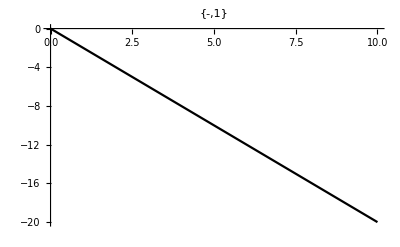
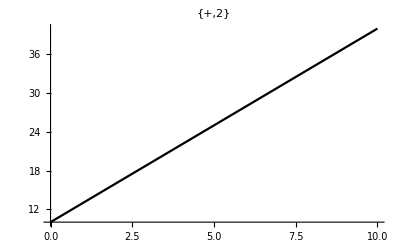
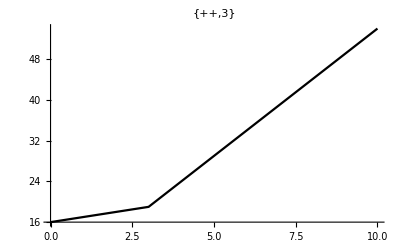
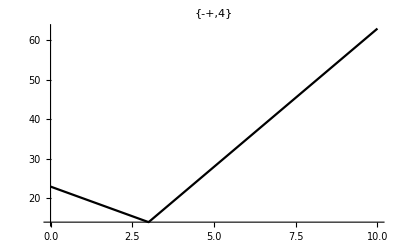
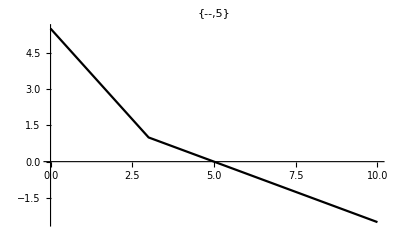
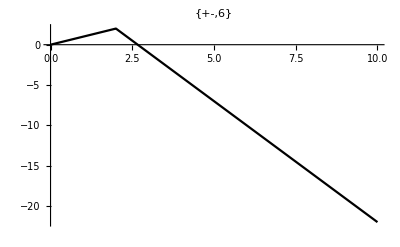

```mathematica
F[1] = Φ[ 1,0,0,3,2];
F[2] = Φ[ 1,0,5,3,2];
F[3] = Φ[1,-2,5,3,2];
F[4] = Φ[1,-5,4,3,2];
F[5] = Φ[1,-0.5,1,3,4];
F[6] = Φ[1,2,1,2,4];
Table[Plot[- F[i],{r,0,10},PlotLabel->{labels[[i]] , i},PlotRange->All,PlotStyle->Black],{i, 1,6}]
```

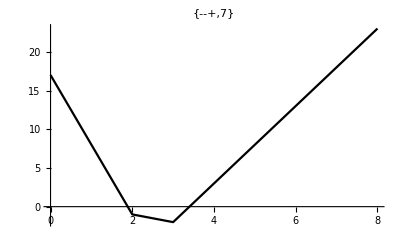
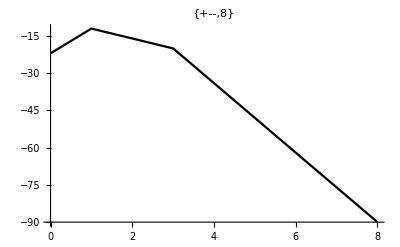
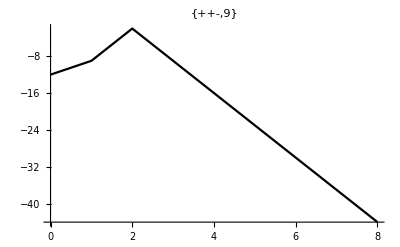
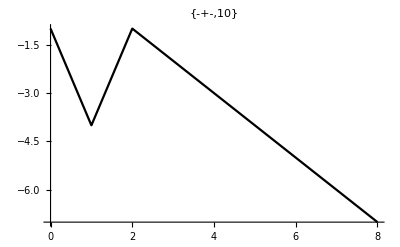
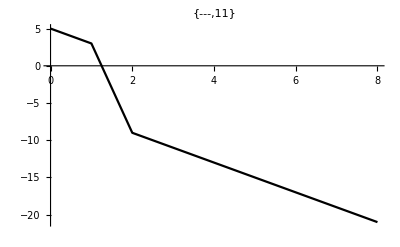
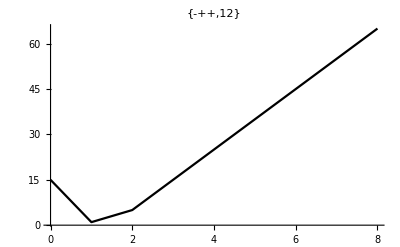

```mathematica
F[7] = Φ[1,-3,4,3,-2];
F[8] = Φ[1,5,-7,3,-1];
F[9] = Φ[1,-2,-7,1,-2];
F[10] = Φ[1,2,3,2,-1];
F[11] = Φ[1,-5,-5,2,-1];
F[12] = Φ[1, -3,9,2,-1];
Table[Plot[- F[i],{r,0, 8},PlotLabel->{labels[[i]] , i},PlotRange->All,PlotStyle->Black],{i, 7,12}]
```

```mathematica
F[13] = Φ[-1,600,595.5,600,-1];
```

```mathematica
-F[13] /.r->0 - (-F[13] /.r->-8)
```

2.69587×10^6

```mathematica
Table[j^(1/i), {i, {1,2,4}}, {j, {1,9}}]
```

```mathematica
-F[13] /.r->12132-(-F[13] /.r->12000)
```

494437.

```mathematica
F[13] = Φ[-1,600,595.50,600,-1];
Table[Plot[- F[13],{r,i, 10},PlotLabel->{labels[[13]] , 13},PlotRange->All], {i,{ 0, 1000}}]
```

Plot::plld: Endpoints for r in {r,i,j} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

```mathematica
RR = k ϵ^-2 δ + ν ϵ^-1 dδ/.k->1/.ϵ->0.1;
```

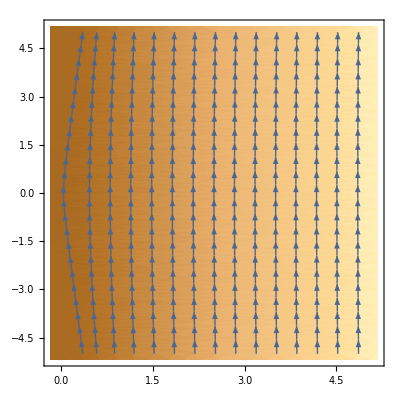

```mathematica
FF[1] = F[1]/.r->RR/. ν->0;
StreamDensityPlot[{dδ,FF[1]}, {δ,0, 5},{dδ,-5, 5}]
```

```mathematica
RR = k ϵ^-2 δ + ν ϵ^-1 dδ/.k->1/.ν->1/.ϵ->0.1
FF[1] = F[1]/.r->RR/.dδ ->0
Solve[{X - FF[1] ==0},δ]
```

100. δ

200. δ

{{δ→0.005 X}}

```mathematica
Reduce[X - F[2] <0,r,Reals]
```

(X≤(-8-8 √3)/(√3)&&r>(8+X)/2)||((-8-8 √3)/(√3)<X≤(8+8 √3)/(√3)&&r>X/(2+2 √3))||(X>(8+8 √3)/(√3)&&r>1/2 (-8+X))

```mathematica
Reduce[X - F[3] <0,r,Reals]
```

(X<(8-8 √3)/(√3)&&r>1/2 (-8+X))||(X==(8-8 √3)/(√3)&&(1/2 (-8+(8-8 √3)/(√3))<r<1/2 (8+(8-8 √3)/(√3))||r>1/2 (8+(8-8 √3)/(√3))))||((8-8 √3)/(√3)<X<(-8+8 √3)/(√3)&&(1/2 (-8+X)<r<-X/(-2+2 √3)||r>(8+X)/2))||(X≥(-8+8 √3)/(√3)&&r>(8+X)/2)

```mathematica
Table[Reduce[X - F[i] <0,r,Reals],{i,1,3}]
```

{r>X/2,(X≤(-8-8 √3)/(√3)&&r>(8+X)/2)||((-8-8 √3)/(√3)<X≤(8+8 √3)/(√3)&&r>X/(2+2 √3))||(X>(8+8 √3)/(√3)&&r>1/2 (-8+X)),(X<(8-8 √3)/(√3)&&r>1/2 (-8+X))||(X==(8-8 √3)/(√3)&&(1/2 (-8+(8-8 √3)/(√3))<r<1/2 (8+(8-8 √3)/(√3))||r>1/2 (8+(8-8 √3)/(√3))))||((8-8 √3)/(√3)<X<(-8+8 √3)/(√3)&&(1/2 (-8+X)<r<-X/(-2+2 √3)||r>(8+X)/2))||(X≥(-8+8 √3)/(√3)&&r>(8+X)/2)}

```mathematica
Table[Solve[X == F[i]],r],{i,1,3}]
Table[Sqrt[Cos[f0] (XX - F[i] )],{i,1,3}]
```

```mathematica
D[Φ[r,σ,  μ1, μ2, Y1, Y2], r]
```

```mathematica
2+σ (1/2 √3 μ1 Abs'[(√3 r)/2-Y1]-1/2 √3 μ2 Abs'[(√3 r)/2+Y2])
```

```mathematica
Solve[X == Φ[r,σ,  μ1, μ2, Y1, Y2],r]
```

```mathematica
{{r->(2 (-√3 X+√3 Y1 μ1 σ-√3 Y2 μ2 σ))/(-4 √3+3 μ1 σ+3 μ2 σ)},{r->(2 (√3 X+√3 Y1 μ1 σ-√3 Y2 μ2 σ))/(4 √3+3 μ1 σ+3 μ2 σ)},{r->(2 (-√3 X+√3 Y1 μ1 σ+√3 Y2 μ2 σ))/(-4 √3+3 μ1 σ-3 μ2 σ)},{r->(2 (√3 X+√3 Y1 μ1 σ+√3 Y2 μ2 σ))/(4 √3+3 μ1 σ-3 μ2 σ)}}
```

```mathematica
Manipulate[
Plot[Φ[r,σ,  μ1, μ2, Y1, Y2],{r,-5,50}], {μ1, -50, 50}, {σ,-1,1},{μ2, -50, 50}, {Y1, 0, 50 },  {Y2, 0, 50 }]
```

```mathematica
Manipulate[Table[StreamDensityPlot[{oo,Cos[f0]( XX - F[i])},{r,-10,20},{oo,-5,5}],{i, 1,5}],{XX, -10, 10}]
```

```mathematica
deltadd[μ1_, μ2_,σ1_, σ2_, X1_, X2_, Y1_, Y2_, ϕ_ ] = (Tan[ϕ]^2 dδ^2)/(1+δ)+Cos[ϕ](X1 - X2 - 2R Cos[ϕ] - (σ1 μ1 Abs[Y1_- R Sin[ϕ]] - σ2 μ2 Abs[Y2 + R Sin[ϕ]]))
```

(dδ^2 Tan[ϕ]^2)/(1+δ)+Cos[ϕ] (X1-X2-μ1 σ1 Abs[-R Sin[ϕ]+Y1_Null]-2 R Cos[ϕ]+σ2 μ2Abs[Y2+R Sin[ϕ]])

```mathematica
deltadd[1] = deltadd[0, 0,1, 1, X1_, X2_, 3, 2,Pi/3]
```

((dδ^2 Tan[ϕ]^2)/(1+δ)+Cos[ϕ] (X1-X2-μ1 σ1 Abs[-R Sin[ϕ]+Y1_Null]-2 R Cos[ϕ]+σ2 μ2Abs[Y2+R Sin[ϕ]]))[0,0,1,1,X1_,X2_,3,2,π/3]

```mathematica
Cos[ϕ] (-2 R Cos[ϕ]+X1-X2-Abs[-R Sin[ϕ]+Y1] μ1 σ1+Abs[R Sin[ϕ]+Y2] μ2 σ2)+(dδ^2 Tan[ϕ]^2)/(1+δ)
```

```mathematica
μ1 = 0
μ2 = 0
```

```mathematica
yy = DSolve[{x1''== X1  - R Cos[ϕ] - μ1 Abs[Y1 - R Sin[ϕ]]σ1,{x2''== X2  + R Cos[ϕ] - μ2 Abs[Y2 + R Sin[ϕ]]σ2, }]
```

```mathematica
f0 = Pi/6;
{d, l,X1, Y1, μ1,X2, Y2, μ2 }={0.8,1, 3.6, 0.8, 0.525, 0, -2.4, 2.85};
ΦΦ:= 2 R + σ(μμ1 Abs[R- YY1]- μμ2 Abs[R + YY2] );
XX = (X1 - X2)/Cos[f0];
YY1 = Y1/Sin[f0];YY2 = Y2/Sin[f0];
μμ1 = μ1 Tan[f0];μμ2 = μ2 Tan[f0];
R= k ϵ^-2 δ + ν ϵ^-1 dδ/.k->1/.ν->1/.ϵ->0.1
```

10. dδ+100. δ

```mathematica
Solve[{Cos[f0]^2(XX - Φ)== 0,  dδ == 0, σ == 1}, δ]
```

{{δ→0.0317586}}

```mathematica
doubleδ = Cos[f0]^2(XX - Φ)/.σ->1
```

3/4 (4.15692-2 (10. dδ+100. δ)+1.64545 Abs[-4.8+10. dδ+100. δ]-0.303109 Abs[-1.6+10. dδ+100. δ])

```mathematica
doubleδ = Simplify[doubleδ/. Abs[-4.8+10. dδ+99.99999999999999 δ]->-4.8+10. dδ+99.99999999999999 δ/.Abs[-1.6+10. dδ+99.99999999999999 δ] ->-1.6+10. dδ+99.99999999999999 δ]
```

-2.44219-4.93245 dδ-49.3245 δ

```mathematica
CC = doubleδ/.dδ ->0 /.δ ->0;
AA = ((doubleδ/.dδ ->0 )- CC)/.δ ->1;
BB =   ((doubleδ/.δ ->0)- CC)/.dδ ->1;
```

```mathematica
BB dδ + AA δ +CC
```

-2.44219-4.93245 dδ-49.3245 δ

```mathematica
Solve[BB λ^2 + AA λ +CC==0, λ]
```

{{λ→-9.95024},{λ→-0.0497603}}

C